```mathematica
SatisfiabilityInstances
```

```mathematica
BooleanConvert[xNE21⧦False,"CNF"]
```

```mathematica
lr
```

```mathematica
bc[sym1_,sym2_]:=BooleanConvert[(sym1/.{0->False,1->True})⧦(sym2/.{0->False,1->True}),"CNF"]
```

```mathematica
xNE21~bc~1
```

xNE21

```mathematica
1+1
```

2

```mathematica
lr
```

!xNE21

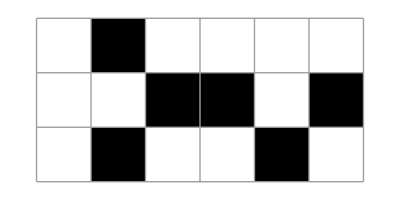
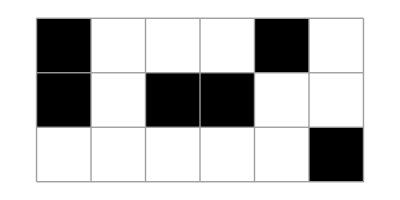
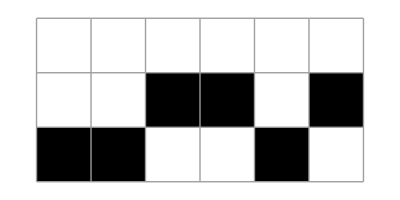
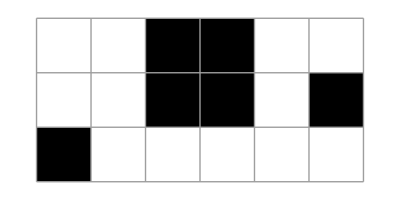
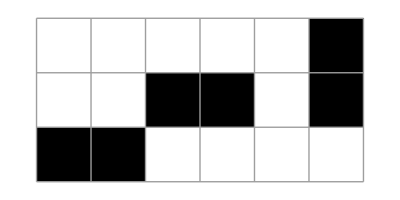
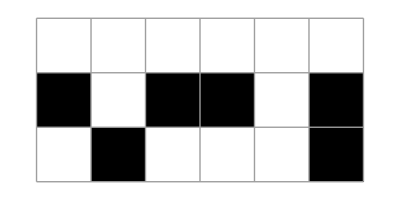
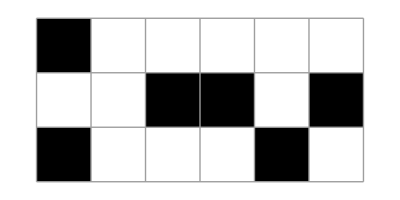
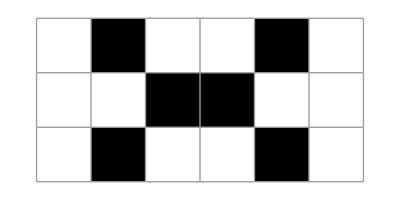

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/02_two_cell_comparison.m"];
looker2=plt[({{xNW21, xN21, xNE21, xNW22, xN22, xNE22}, {xW21, x21, xE21, xW22, x22, xE22}, {xSW21, xS21, xSE21, xSW22, xS22, xSE22}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)

looker2/@endGame
```

```mathematica
Implies
```

```mathematica
⇒
```

```mathematica
cnf[x⇒False]
```

CNF | DNF
¬x | ¬x

```mathematica
life44
```

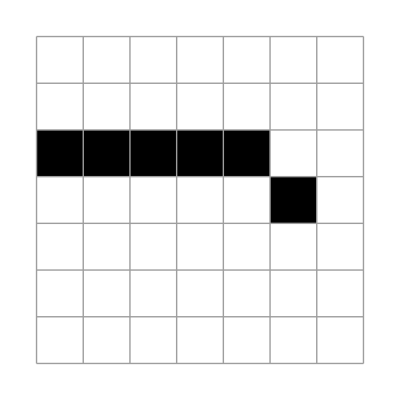
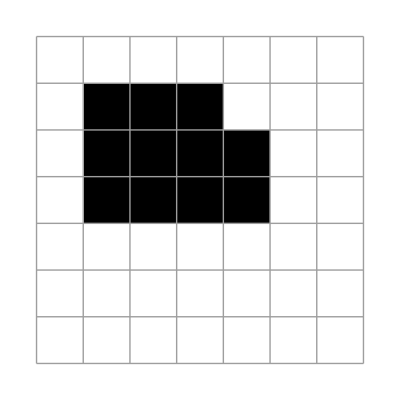
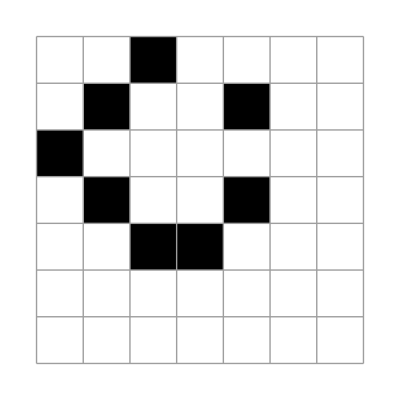
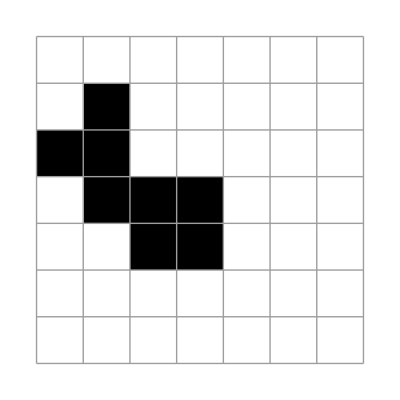

```mathematica
X0=({{0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}, {xNW21, xN21, xNE21, xNW22, xN22, xNE22, 0}, {xW21, x21, xE21, xW22, x22, xE22, 0}, {xSW21, xS21, xSE21, xSW22, xS22, xSE22, 0}, {0, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0}})/.endGame[[1]];
plt/@NestList[updateLife2[{7,7}][ #]&,
X0,3]
```